```mathematica
delPhi = 1/8;
d=3;
Clear[d,delPhi]
```

```mathematica
rhoNu= ( (2^(l-1)Gamma[l+d/2])/(Pi^(d/2)Gamma[l+1])Gamma[d/2-delPhi]^2/Gamma[delPhi]^2 1/(Gamma[del-d/2]Gamma[d-del-d/2])(del+l-1)(d-del+l-1)Gamma[del-1]Gamma[d-del-1] ((Gamma[(l-del+2delPhi)/2]Gamma[(l-d+del+2delPhi)/2])/(Gamma[(d+l+del-2 delPhi)/2]Gamma[(d+l+d-del-2 delPhi)/2])))/.{l->0,del->d/2+I nu};
kNu= (2^(2l) (Gamma[(del+l)/2]^2 Gamma[(d-del+l)/2]^2))/(l! Pochhammer[d/2-1,l]Gamma[del-d/2]Gamma[d/2-del]) (Gamma[delPhi - (del-l)/2]^2 Gamma[delPhi - (d-del-l)/2]^2)/(Pochhammer[del-1,l]Pochhammer[d-del-1,l])/.{l->0,del->d/2+I nu};
Ndel = 1/(4 Pi Pi^(d/2))Gamma[d/2-del]Gamma[del];
```

```mathematica
rhoNu/.nu->1//N;
```

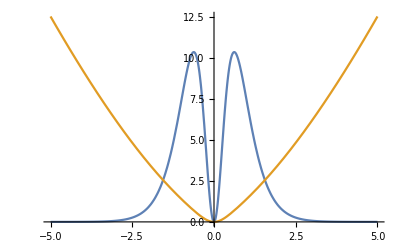

```mathematica
Plot[{kNu/.{nu->x,d->3,delPhi->1.1},rhoNu/.{nu->x,d->3,delPhi->1.1}},{x,-5,5}]
```

```mathematica
param=Ndel^2/(4 Gamma[delPhi]^4)Sin[Pi/2(4 delPhi -d)]/.{del->delPhi}
```

(π^(-2-d) Gamma[d/2-delPhi]^2 Sin[1/2 (-d+4 delPhi) π])/(64 Gamma[delPhi]^2)

```mathematica
param/.{d->3,delPhi->0.001}//N
```

4.01441×10^-11

```mathematica
Limit[ kNu/.{d->3,nu->0},delPhi->3/4]
```

0

```mathematica
param kNu/.{d->3,delPhi->3/4}
```

0

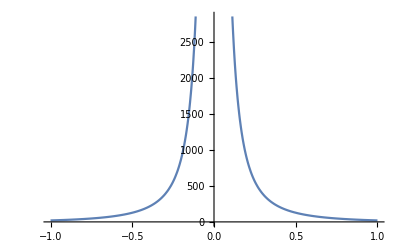

```mathematica
Plot[ kNu/.{d->3,delPhi->3/4,nu->x},{x,-1,1}]
```

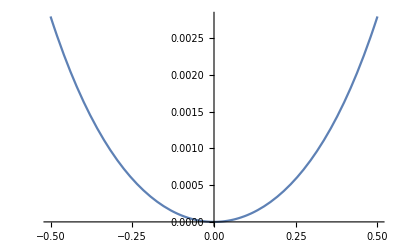

```mathematica
Plot[rhoNu/( kNu)/.{nu->x,d->3,delPhi->3/4},{x,-0.5,0.5}]
```

```mathematica
Limit[Limit[rhoNu/( param kNu)/.{nu->x,d->3,delPhi->y},x->0],y->0.1]//N
```

37.9821

```mathematica
plot3=Plot[rhoNu/kNu/.{nu->0.000001,d->3,delPhi->x},{x,0.000001,0.01},Filling->Bottom,FillingStyle->LightRed,AxesLabel->{"Δ_ϕ^-"}];
plot1=Plot[rhoNu/kNu/.{nu->0.000001,d->3,delPhi->x},{x,0.000001,0.88-0.000001},Filling->Bottom,FillingStyle->LightRed,AxesLabel->{"Δ_ϕ^-"}];
plot2=Plot[rhoNu/kNu/.{nu->0.000001,d->3,delPhi->x},{x,0.88-0.000001,3/2-0.000001},Filling->Bottom,FillingStyle->LightRed,AxesLabel->{"Δ_ϕ^-"}];
```

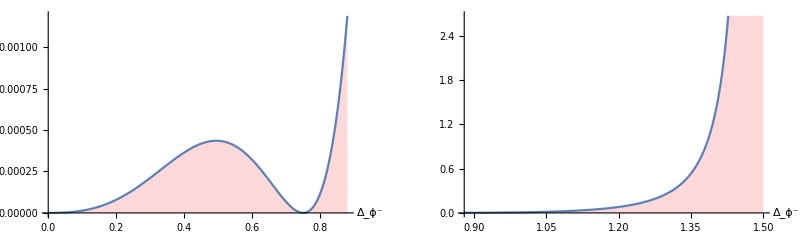

```mathematica
GraphicsGrid[{{plot1,plot2}},PlotLabel->{"lol"},Spacings->{30, 30}]
```

```mathematica
Ndel
```

1/4 π^(-1-d/2) Gamma[d/2-del] Gamma[del]

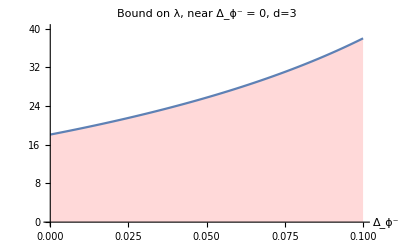

```mathematica
plot=Plot[rhoNu/(param kNu)/.{nu->0.0000001,d->3,delPhi->x},{x,0.00000,0.1},Filling->Bottom,FillingStyle->LightRed,AxesLabel->{"Δ_ϕ^-"},PlotRange->{{0,0.1},{0,40}},PlotLabel->"Bound on λ, near Δ_ϕ^- = 0, d=3"]
```

```mathematica
rhoNu/.{nu->0.000000001,d->3,delPhi->3/4}//N
 kNu/.{nu->0.00001,d->3,delPhi->3/4}//N
param /.{nu->0.00001,d->3,delPhi->3/4}//N
```

0.31831+1.3165×10^-25 ⅈ

3.60791×10^11+9.31323×10^-10 ⅈ

0.

```mathematica
kNu
```

(Gamma[delPhi+1/2 (-d/2-ⅈ nu)]^2 Gamma[delPhi+1/2 (-d/2+ⅈ nu)]^2 Gamma[1/2 (d/2-ⅈ nu)]^2 Gamma[1/2 (d/2+ⅈ nu)]^2)/(Gamma[-ⅈ nu] Gamma[ⅈ nu])